## (#1): Static Quantities:

## (#1.1): Mass of Proton:

```mathematica
MassOfProton=Quantity[.93827208816,"Gigaelectronvolts"];
```

## (#1.2): F_E Constant:

```mathematica
ElectricFormFactorConstant=Quantity[0.710649,"Gigaelectronvolts Squared"];
```

## (#1.3): α_EM:

```mathematica
ElectromagneticFineStructureConstant=1/137.035999177;
```

## (#1.4): Proton Magnetic Moment

```mathematica
ProtonMagneticMoment=2.79284734463;
```

## (#1.5): Kinematic “Bins”:

### (#1.5.1): Q^2 (photon virtuality)

```mathematica
qSquared=Quantity[1.8200000524520876,"Gigaelectronvolts Squared"];
```

### (#1.5.2): x_B (Bjorken x)

```mathematica
xBjorken=0.3429999947547912;
```

### (#1.5.3): t (hadron momentum transfer squared)

```mathematica
hadronMomentumT=Quantity[-0.1720000058412552,"Gigaelectronvolts Squared"];
```

### (#1.5.4): k (incident beam energy)

```mathematica
incidentBeamK=Quantity[5.75,"Gigaelectronvolts"];
```

### (#1.5.5): λ (lepton beam helicity)

```mathematica
leptonλPlus=1/2;
leptonλMinus=-1/2;
```

### (#1.5.6): Λ (target polarization)

```mathematica
unpolarizedTargetΛ=0;
longitudinallyPolarizedTargetΛ=1;
```

```mathematica
Realℋ=-0.897;
RealℋT=2.444;
Realℰ=-0.541;
RealℰT=2.207;
Imaginaryℋ=2.421;
ImaginaryℋT=1.131;
Imaginaryℰ=0.903;
ImaginaryℰT=5.383;
ℋ=Realℋ+I Imaginaryℋ;
ℋT=RealℋT+I ImaginaryℋT;
ℰ=Realℰ+I Imaginaryℰ;
ℰT=RealℰT+I ImaginaryℰT;
```

```mathematica
ConvertGeVMinus6ToNbGevMinus4[ValueInGeVMinus6_]:=Quantity[.389379*1000000*ValueInGeVMinus6,("Nanobarns"*"Gigaelectronvolts"*"Gigaelectronvolts")];
```

## (#1.4): Proton Magnetic Moment

## (#2): Derived Quantities:

## (#2.1.1): Derived Kinematics | ϵ

```mathematica
Epsilon[qSquared_,xB_]:=2xB(MassOfProton/(√qSquared));
ϵKinematics=Epsilon[qSquared,xBjorken]
```

0.477109

```mathematica
0.4771085571437671^2
```

0.227633

## (#2.1.2): Derived Kinematics | y

```mathematica
LeptonEnergyFraction[qSquared_,k_,ϵ_]:=(√qSquared)/(ϵ k);
```

```mathematica
yKinematics=LeptonEnergyFraction[qSquared,incidentBeamK,ϵKinematics]
```

0.491757

## (#2.1.3): Derived Kinematics | ξ

```mathematica
SkewnessParameter[qSquared_,xB_,t_]:=xB((1+t/(2*qSquared))/(2-xB+(xB t)/qSquared));
ξSkewness=SkewnessParameter[qSquared,xBjorken,hadronMomentumT]
```

0.201154

## (#2.1.4): Derived Kinematics | t_min

```mathematica
tMinimum[qSquared_,xB_,ϵ_]:=-qSquared*((2(1-xB)(1 - √(1 + ϵ^2)) + ϵ^2)/(4 xB (1-xB)+ ϵ^2));
tMinKinematics=tMinimum[qSquared,xBjorken,ϵKinematics]
```

-0.138211 GeV^2

## (#2.1.5): Derived Kinematics | t'

```mathematica
tPrime[t_,tMinimum_]:=t-tMinimum;
tPrimeKinematics=tPrime[hadronMomentumT,tMinKinematics]
```

-0.0337889 GeV^2

## (#2.1.6): Derived Kinematics | K̃

```mathematica
kTilde[qSquared_,xB_,y_,t_,ϵ_,tMin_]:=√(tMin-t)√((1-xB)√(1+ϵ^2)+((tMin-t)(ϵ^2+4(1-xB)xB))/(4qSquared))(√(1-y-ϵ^2/4 y^2))/(√(1-y+ϵ^2/4 y^2));
kTildeKinematics=kTilde[qSquared,xBjorken,yKinematics,hadronMomentumT,ϵKinematics,tMinKinematics]
```

0.153191 GeV

```mathematica
Quantity[0.1573963123403191, "Gigaelectronvolts"]-Quantity[0.15319062268109196, "Gigaelectronvolts"]
```

0.00420569 GeV

## (#2.1.7): Derived Kinematics | K

```mathematica
KinematicK[qSquared_,y_,ϵ_,kTilde_]:=kTilde√((1-y+(ϵ^2 y^2)/4)/qSquared);
KKinematics=KinematicK[qSquared,yKinematics,ϵKinematics,kTildeKinematics]
```

0.0820415

## (#2.2.1): Derived Form Factors | F_E

```mathematica
ElectricFormFactor[t_]:=1/(1-t/ElectricFormFactorConstant)^2;
FE=ElectricFormFactor[hadronMomentumT]
```

0.648238

## (#2.2.2): Derived Form Factors | F_G

```mathematica
MagneticFormFactor[FE_]:=ProtonMagneticMoment*FE;
FG=MagneticFormFactor[0.6482376115457034]
```

1.81043

## (#2.2.3): Derived Form Factors | F_2

```mathematica
PauliFormFactor[t_,FElectric_,FMagnetic_]:=(FMagnetic-FElectric)/(1+(-t)/(4 MassOfProton^2));
F2=PauliFormFactor[hadronMomentumT,FE,FG]
```

1.10807

## (#2.2.4): Derived Form Factors | F_1

```mathematica
DiracFormFactor[t_,FMagnetic_,F2Pauli_]:=FMagnetic-F2Pauli;
F1=DiracFormFactor[hadronMomentumT,FG,F2]
```

0.70236

## (#2.2.5): Derived Form Factors | ℱ_eff

```mathematica
EffectiveFormFactor[ξ_,ℱ_]:=-2ξ ℱ(1/(1+ξ));
EffectiveFormFactor[ξSkewness,Realℋ]
EffectiveFormFactor[ξSkewness,RealℋT]
EffectiveFormFactor[ξSkewness,Realℰ]
EffectiveFormFactor[ξSkewness,RealℰT]
EffectiveFormFactor[ξSkewness,Imaginaryℋ]
EffectiveFormFactor[ξSkewness,ImaginaryℋT]
EffectiveFormFactor[ξSkewness,Imaginaryℰ]
EffectiveFormFactor[ξSkewness,ImaginaryℰT]
```

0.300437

-0.818581

0.1812

-0.739202

-0.810878

-0.378812

-0.302446

-1.80296

```mathematica
CrossSectionPrefactor[qSquared_,xB_,ϵ_,y_]:=(ElectromagneticFineStructureConstant^3 y^2 xB)/(8 π qSquared^2 √(1+ϵ^2))
```

## (#3): Derived Quantities: BH Coefficients

## (#4): Derived Quantities: DVCS Coefficients

## (#4.1.1): (𝒞^DVCS)_unp(ℱ, ℱ^*):

```mathematica
CurlyCDVCSUnp[qSquared_,xB_,t_,ϵ_,ℋ_,ℋT_,ℰ_,ℰT_,ℋConjugate_,ℋTConjugate_,ℰConjugate_,ℰTConjugate_]:= ((qSquared(qSquared+xB t))/((2-xB)qSquared+xB t)^2)(4(1-xB )ℋ ℋConjugate +4(1-xB+((2qSquared+t)/(qSquared+xB t))(ϵ^2/4))ℋT ℋTConjugate-((xB^2(qSquared+t)^2)/(qSquared(qSquared+xB t)))(ℋ ℰConjugate+ℰ ℋConjugate)-((xB^2 qSquared)/(qSquared+xB t))(ℋT ℰTConjugate+ℰT ℋTConjugate)-((xB^2(qSquared+t)^2)/(qSquared(qSquared+xB t))+(((2-xB)qSquared+xB t)^2/(qSquared(qSquared+xB t)))(t/(4 MassOfProton^2)))ℰ ℰConjugate-((xB^2 qSquared)/(qSquared+xB t))(t/(4 MassOfProton^2))ℰT ℰTConjugate);
```

### (#4.1.1.1): Testing (𝒞^DVCS)_unp(ℱ, ℱ^*):

```mathematica
CurlyCDVCSUnp[qSquared,xBjorken,hadronMomentumT,ϵKinematics,ℋ,ℋT,ℰ,ℰT,Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT]]
```

13.4697-1.27193×10^-18 ⅈ

### (#4.1.1.2): Testing (𝒞^DVCS)_unp(ℱ_eff, ℱ_eff^*):

First, we are computing ℱ_eff then conjugating.

```mathematica
CurlyCDVCSUnp[qSquared,xBjorken,hadronMomentumT,ϵKinematics,EffectiveFormFactor[ξSkewness,ℋ],EffectiveFormFactor[ξSkewness,ℋT],EffectiveFormFactor[ξSkewness,ℰ],EffectiveFormFactor[ξSkewness,ℰT],Conjugate[EffectiveFormFactor[ξSkewness,ℋ]],Conjugate[EffectiveFormFactor[ξSkewness,ℋT]],Conjugate[EffectiveFormFactor[ξSkewness,ℰ]],Conjugate[EffectiveFormFactor[ξSkewness,ℰT]]]
```

1.51105+0. ⅈ

Now, we are conjugating ℱ then getting ℱ_eff.

```mathematica
CurlyCDVCSUnp[qSquared,xBjorken,hadronMomentumT,ϵKinematics,EffectiveFormFactor[ξSkewness,ℋ],EffectiveFormFactor[ξSkewness,ℋT],EffectiveFormFactor[ξSkewness,ℰ],EffectiveFormFactor[ξSkewness,ℰT],Conjugate[EffectiveFormFactor[ξSkewness,ℋ]],Conjugate[EffectiveFormFactor[ξSkewness,ℋT]],Conjugate[EffectiveFormFactor[ξSkewness,ℰ]],Conjugate[EffectiveFormFactor[ξSkewness,ℰT]]]
```

1.51105+0. ⅈ

## (#4.1.2): (𝒞^DVCS)_LP(ℱ, ℱ^*):

```mathematica
CurlyCDVCSLP[qSquared_,xB_,t_,ϵ_,ℋ_,ℋT_,ℰ_,ℰT_,ℋConjugate_,ℋTConjugate_,ℰConjugate_,ℰTConjugate_]:=((qSquared(qSquared+xB t))/(√(1+ϵ^2)((2-xB)qSquared+xB t)^2))(4(1-xB+(((3-2xB)qSquared+t)/(qSquared+xB t)) (ϵ^2/4))(ℋ ℋTConjugate+ℋT ℋConjugate)-((qSquared-xB(1-2xB)t)/(qSquared+xB t))xB^2(ℋ ℰTConjugate+ℰT ℋConjugate+ℋT ℰConjugate+ℰ ℋTConjugate)-((4(1-xB)(qSquared+xB t)t+(qSquared+t)^2 ϵ^2)/(2 qSquared(qSquared+xB t)))xB(ℋT ℰConjugate+ℰ ℋTConjugate)-(((2-xB)qSquared+xB t)/(qSquared+xB t))((xB^2(qSquared+t)^2)/(2qSquared((2-xB)qSquared+xB t))+t/(4 MassOfProton^2))xB (ℰ ℰTConjugate+ℰT ℰConjugate));
```

### (#4.1.1.1): Testing (𝒞^DVCS)_LP(ℱ, ℱ^*):

## (#4.2.1): c_o^DVCS:

```mathematica
cODVCS[λ_,Λ_,qSquared_,xB_,t_,ϵ_,y_,K_,ℋ_,ℋT_,ℰ_,ℰT_,ℋConjugate_,ℋTConjugate_,ℰConjugate_,ℰTConjugate_, ℋeff_,ℋTeff_,ℰeff_,ℰTeff_,ℋConjugateeff_,ℋTConjugateeff_,ℰConjugateeff_,ℰTConjugateeff_]:=
If[Λ==1,
((2λ Λ y(2-y))/(√(1+ϵ^2)))CurlyCDVCSLP[qSquared,xB,t,ϵ,ℋ,ℋT,ℰ,ℰT,ℋConjugate,ℋTConjugate,ℰConjugate,ℰTConjugate],
2 ((2-2y+y^2+(ϵ^2/2)y^2)/(1+ϵ^2))CurlyCDVCSUnp[qSquared,xB,t,ϵ,ℋ,ℋT,ℰ,ℰT,ℋConjugate,ℋTConjugate,ℰConjugate,ℰTConjugate]+((16 K^2)/((2-xB)^2(1+ϵ^2)))CurlyCDVCSUnp[qSquared,xB,t,ϵ,ℋeff,ℋTeff,ℰeff,ℰTeff,ℋConjugateeff,ℋTConjugateeff,ℰConjugateeff,ℰTConjugateeff]
];
```

### (#4.2.1.1): Testing c_o^DVCS | (+) Polarized Beam / Unpolarized Target:

```mathematica
cODVCS[leptonλPlus,unpolarizedTargetΛ,qSquared,xBjorken,hadronMomentumT,ϵKinematics,yKinematics,KKinematics,ℋ,ℋT,ℰ,ℰT,Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT],EffectiveFormFactor[ξSkewness,ℋ],EffectiveFormFactor[ξSkewness,ℋT],EffectiveFormFactor[ξSkewness,ℰ],EffectiveFormFactor[ξSkewness,ℰT],EffectiveFormFactor[ξSkewness,Conjugate[ℋ]],EffectiveFormFactor[ξSkewness,Conjugate[ℋT]],EffectiveFormFactor[ξSkewness,Conjugate[ℰ]],EffectiveFormFactor[ξSkewness,Conjugate[ℰT]]]
```

28.2649-2.66447×10^-18 ⅈ

### (#4.2.1.2): Testing c_o^DVCS | (-) Polarized Beam / Unpolarized Target:

```mathematica
cODVCS[leptonλMinus,unpolarizedTargetΛ,qSquared,xBjorken,hadronMomentumT,ϵKinematics,yKinematics,KKinematics,ℋ,ℋT,ℰ,ℰT,Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT],EffectiveFormFactor[ξSkewness,ℋ],EffectiveFormFactor[ξSkewness,ℋT],EffectiveFormFactor[ξSkewness,ℰ],EffectiveFormFactor[ξSkewness,ℰT],EffectiveFormFactor[ξSkewness,Conjugate[ℋ]],EffectiveFormFactor[ξSkewness,Conjugate[ℋT]],EffectiveFormFactor[ξSkewness,Conjugate[ℰ]],EffectiveFormFactor[ξSkewness,Conjugate[ℰT]]]
```

28.2649-2.66447×10^-18 ⅈ

### (#4.2.1.3): Testing c_o^DVCS | (+) Polarized Beam / Longitudinally-Polarized Target:

```mathematica
cODVCS[leptonλPlus,longitudinallyPolarizedTargetΛ,qSquared,xBjorken,hadronMomentumT,ϵKinematics,yKinematics,KKinematics,ℋ,ℋT,ℰ,ℰT,Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT],EffectiveFormFactor[ξSkewness,ℋ],EffectiveFormFactor[ξSkewness,ℋT],EffectiveFormFactor[ξSkewness,ℰ],EffectiveFormFactor[ξSkewness,ℰT],EffectiveFormFactor[ξSkewness,Conjugate[ℋ]],EffectiveFormFactor[ξSkewness,Conjugate[ℋT]],EffectiveFormFactor[ξSkewness,Conjugate[ℰ]],EffectiveFormFactor[ξSkewness,Conjugate[ℰT]]]
```

0.193407+0. ⅈ

### (#4.2.1.4): Testing c_o^DVCS | (-) Polarized Beam / Longitudinally-Polarized Target:

```mathematica
cODVCS[leptonλMinus,longitudinallyPolarizedTargetΛ,qSquared,xBjorken,hadronMomentumT,ϵKinematics,yKinematics,KKinematics,ℋ,ℋT,ℰ,ℰT,Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT],EffectiveFormFactor[ξSkewness,ℋ],EffectiveFormFactor[ξSkewness,ℋT],EffectiveFormFactor[ξSkewness,ℰ],EffectiveFormFactor[ξSkewness,ℰT],EffectiveFormFactor[ξSkewness,Conjugate[ℋ]],EffectiveFormFactor[ξSkewness,Conjugate[ℋT]],EffectiveFormFactor[ξSkewness,Conjugate[ℰ]],EffectiveFormFactor[ξSkewness,Conjugate[ℰT]]]
```

-0.193407+0. ⅈ

## (#4.2.2): c_1^DVCS:

```mathematica
c1DVCS[λ_,Λ_,qSquared_,xB_,t_,ϵ_,y_,K_,ℋeff_,ℋTeff_,ℰeff_,ℰTeff_,ℋConjugate_,ℋTConjugate_,ℰConjugate_,ℰTConjugate_]:=
If[Λ==1,
-((8Λ K)/((2-xB)(1+ϵ^2)))(-λ y √(1+ϵ^2)) Re[CurlyCDVCSLP[qSquared,xB,t,ϵ,ℋeff,ℋTeff,ℰeff,ℰTeff,ℋConjugate,ℋTConjugate,ℰConjugate,ℰTConjugate]],
((8K)/((2-xB)(1+ϵ^2)))(2-y)Re[CurlyCDVCSUnp[qSquared,xB,t,ϵ,ℋeff,ℋTeff,ℰeff,ℰTeff,ℋConjugate,ℋTConjugate,ℰConjugate,ℰTConjugate]]
];
```

### (#4.2.2.1): Testing c_1^DVCS | (+) Polarized Beam / Unpolarized Target:

```mathematica
c1DVCS[leptonλPlus,unpolarizedTargetΛ,qSquared,xBjorken,hadronMomentumT,ϵKinematics,yKinematics,KKinematics,EffectiveFormFactor[ξSkewness,ℋ],EffectiveFormFactor[ξSkewness,ℋT],EffectiveFormFactor[ξSkewness,ℰ],EffectiveFormFactor[ξSkewness,ℰT],Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT]]
```

-2.19545

### (#4.2.2.2): Testing c_1^DVCS | (-) Polarized Beam / Unpolarized Target:

```mathematica
c1DVCS[leptonλMinus,unpolarizedTargetΛ,qSquared,xBjorken,hadronMomentumT,ϵKinematics,yKinematics,KKinematics,EffectiveFormFactor[ξSkewness,ℋ],EffectiveFormFactor[ξSkewness,ℋT],EffectiveFormFactor[ξSkewness,ℰ],EffectiveFormFactor[ξSkewness,ℰT],Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT]]
```

-2.19545

### (#4.2.2.3): Testing c_1^DVCS | (+) Polarized Beam / Longitudinally-Polarized Target:

```mathematica
c1DVCS[leptonλPlus,longitudinallyPolarizedTargetΛ,qSquared,xBjorken,hadronMomentumT,ϵKinematics,yKinematics,KKinematics,EffectiveFormFactor[ξSkewness,ℋ],EffectiveFormFactor[ξSkewness,ℋT],EffectiveFormFactor[ξSkewness,ℰ],EffectiveFormFactor[ξSkewness,ℰT],Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT]]
```

-0.00850616

### (#4.2.2.4): Testing c_1^DVCS | (-) Polarized Beam / Longitudinally-Polarized Target:

```mathematica
c1DVCS[leptonλMinus,longitudinallyPolarizedTargetΛ,qSquared,xBjorken,hadronMomentumT,ϵKinematics,yKinematics,KKinematics,EffectiveFormFactor[ξSkewness,ℋ],EffectiveFormFactor[ξSkewness,ℋT],EffectiveFormFactor[ξSkewness,ℰ],EffectiveFormFactor[ξSkewness,ℰT],Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT]]
```

0.00850616

## (#4.2.3): c_2^DVCS:

```mathematica
c2DVCS[λ_,Λ_,qSquared_,xB_,t_,ϵ_,y_,K_,ℋ_,ℋT_,ℰ_,ℰT_,ℋConjugate_,ℋTConjugate_,ℰConjugate_,ℰTConjugate_]:=0;
```

### (#4.2.2.4): Testing c_1^DVCS | (+) Polarized Beam / Unpolarized Target:

```mathematica
c2DVCS[leptonλPlus,unpolarizedTargetΛ,qSquared,xBjorken,hadronMomentumT,ϵKinematics,yKinematics,KKinematics,F1,F2,EffectiveFormFactor[ξSkewness,ℋ],EffectiveFormFactor[ξSkewness,ℋT],EffectiveFormFactor[ξSkewness,ℰ],EffectiveFormFactor[ξSkewness,ℰT],Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT]]
```

c2DVCS[1/2,0,1.82 GeV^2,0.343,-0.172 GeV^2,0.477109,0.491757,0.0820415,0.70236,1.10807,0.300437-0.810878 ⅈ,-0.818581-0.378812 ⅈ,0.1812-0.302446 ⅈ,-0.739202-1.80296 ⅈ,-0.897-2.421 ⅈ,2.444-1.131 ⅈ,-0.541-0.903 ⅈ,2.207-5.383 ⅈ]

### (#4.2.2.4): Testing c_1^DVCS | (-) Polarized Beam / Longitudinally-Polarized Target:

```mathematica
c2DVCS[leptonλMinus,unpolarizedTargetΛ,qSquared,xBjorken,hadronMomentumT,ϵKinematics,yKinematics,KKinematics,F1,F2,EffectiveFormFactor[ξSkewness,ℋ],EffectiveFormFactor[ξSkewness,ℋT],EffectiveFormFactor[ξSkewness,ℰ],EffectiveFormFactor[ξSkewness,ℰT],Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT]]
```

c2DVCS[-1/2,0,1.82 GeV^2,0.343,-0.172 GeV^2,0.477109,0.491757,0.0820415,0.70236,1.10807,0.300437-0.810878 ⅈ,-0.818581-0.378812 ⅈ,0.1812-0.302446 ⅈ,-0.739202-1.80296 ⅈ,-0.897-2.421 ⅈ,2.444-1.131 ⅈ,-0.541-0.903 ⅈ,2.207-5.383 ⅈ]

### (#4.2.2.4): Testing c_1^DVCS | (+) Polarized Beam / Longitudinally-Polarized Target:

```mathematica
c2DVCS[leptonλPlus,longitudinallyPolarizedTargetΛ,qSquared,xBjorken,hadronMomentumT,ϵKinematics,yKinematics,KKinematics,F1,F2,EffectiveFormFactor[ξSkewness,ℋ],EffectiveFormFactor[ξSkewness,ℋT],EffectiveFormFactor[ξSkewness,ℰ],EffectiveFormFactor[ξSkewness,ℰT],Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT]]
```

c2DVCS[1/2,1,1.82 GeV^2,0.343,-0.172 GeV^2,0.477109,0.491757,0.0820415,0.70236,1.10807,0.300437-0.810878 ⅈ,-0.818581-0.378812 ⅈ,0.1812-0.302446 ⅈ,-0.739202-1.80296 ⅈ,-0.897-2.421 ⅈ,2.444-1.131 ⅈ,-0.541-0.903 ⅈ,2.207-5.383 ⅈ]

### (#4.2.2.4): Testing c_1^DVCS | (-) Polarized Beam / Longitudinally-Polarized Target:

```mathematica
c2DVCS[leptonλMinus,longitudinallyPolarizedTargetΛ,qSquared,xBjorken,hadronMomentumT,ϵKinematics,yKinematics,KKinematics,F1,F2,EffectiveFormFactor[ξSkewness,ℋ],EffectiveFormFactor[ξSkewness,ℋT],EffectiveFormFactor[ξSkewness,ℰ],EffectiveFormFactor[ξSkewness,ℰT],Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT]]
```

c2DVCS[-1/2,1,1.82 GeV^2,0.343,-0.172 GeV^2,0.477109,0.491757,0.0820415,0.70236,1.10807,0.300437-0.810878 ⅈ,-0.818581-0.378812 ⅈ,0.1812-0.302446 ⅈ,-0.739202-1.80296 ⅈ,-0.897-2.421 ⅈ,2.444-1.131 ⅈ,-0.541-0.903 ⅈ,2.207-5.383 ⅈ]

## (#4.2.4): s_1^DVCS:

```mathematica
s1DVCS[λ_,Λ_,qSquared_,xB_,t_,ϵ_,y_,K_,ℋeff_,ℋTeff_,ℰeff_,ℰTeff_,ℋConjugate_,ℋTConjugate_,ℰConjugate_,ℰTConjugate_]:=
If[Λ==1,
-((8Λ K)/((2-xB)(1+ϵ^2)))(2-y) Im[CurlyCDVCSLP[qSquared,xB,t,ϵ,ℋeff,ℋTeff,ℰeff,ℰTeff,ℋConjugate,ℋTConjugate,ℰConjugate,ℰTConjugate]],
((8K)/((2-xB)(1+ϵ^2)))(-λ y√(1+ϵ^2))Im[CurlyCDVCSUnp[qSquared,xB,t,ϵ,ℋeff,ℋTeff,ℰeff,ℰTeff,ℋConjugate,ℋTConjugate,ℰConjugate,ℰTConjugate]]
];
```

### (#4.2.2.1): Testing s_1^DVCS | (+) Polarized Beam / Unpolarized Target:

```mathematica
s1DVCS[leptonλPlus,unpolarizedTargetΛ,qSquared,xBjorken,hadronMomentumT,ϵKinematics,yKinematics,KKinematics,EffectiveFormFactor[ξSkewness,ℋ],EffectiveFormFactor[ξSkewness,ℋT],EffectiveFormFactor[ξSkewness,ℰ],EffectiveFormFactor[ξSkewness,ℰT],Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT]]
```

1.42227×10^-17

### (#4.2.2.2): Testing s_1^DVCS | (-) Polarized Beam / Unpolarized Target:

```mathematica
s1DVCS[leptonλMinus,unpolarizedTargetΛ,qSquared,xBjorken,hadronMomentumT,ϵKinematics,yKinematics,KKinematics,EffectiveFormFactor[ξSkewness,ℋ],EffectiveFormFactor[ξSkewness,ℋT],EffectiveFormFactor[ξSkewness,ℰ],EffectiveFormFactor[ξSkewness,ℰT],Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT]]
```

-1.42227×10^-17

### (#4.2.2.3): Testing s_1^DVCS | (+) Polarized Beam / Longitudinally-Polarized Target:

```mathematica
s1DVCS[leptonλPlus,longitudinallyPolarizedTargetΛ,qSquared,xBjorken,hadronMomentumT,ϵKinematics,yKinematics,KKinematics,EffectiveFormFactor[ξSkewness,ℋ],EffectiveFormFactor[ξSkewness,ℋT],EffectiveFormFactor[ξSkewness,ℰ],EffectiveFormFactor[ξSkewness,ℰT],Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT]]
```

-2.22836×10^-16

### (#4.2.2.4): Testing s_1^DVCS | (-) Polarized Beam / Longitudinally-Polarized Target:

```mathematica
s1DVCS[leptonλMinus,longitudinallyPolarizedTargetΛ,qSquared,xBjorken,hadronMomentumT,ϵKinematics,yKinematics,KKinematics,EffectiveFormFactor[ξSkewness,ℋ],EffectiveFormFactor[ξSkewness,ℋT],EffectiveFormFactor[ξSkewness,ℰ],EffectiveFormFactor[ξSkewness,ℰT],Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT]]
```

-2.22836×10^-16

## (#4.2.5): s_2^DVCS:

```mathematica
s2DVCS[λ_,Λ_,qSquared_,xB_,t_,ϵ_,y_,K_,ℋ_,ℋT_,ℰ_,ℰT_,ℋConjugate_,ℋTConjugate_,ℰConjugate_,ℰTConjugate_]:=0;
```

### (#4.2.5.1): Testing s_2^DVCS | (+) Polarized Beam / Unpolarized Target:

```mathematica
s2DVCS[leptonλPlus,unpolarizedTargetΛ,qSquared,xBjorken,hadronMomentumT,ϵKinematics,yKinematics,KKinematics,F1,F2,ℋ,ℋT,ℰ,ℰT,Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT]]
```

s2DVCS[1/2,0,1.82 GeV^2,0.343,-0.172 GeV^2,0.477109,0.491757,0.0820415,0.70236,1.10807,-0.897+2.421 ⅈ,2.444+1.131 ⅈ,-0.541+0.903 ⅈ,2.207+5.383 ⅈ,-0.897-2.421 ⅈ,2.444-1.131 ⅈ,-0.541-0.903 ⅈ,2.207-5.383 ⅈ]

### (#4.2.5.2): Testing s_2^DVCS | (-) Polarized Beam / Unpolarized Target:

```mathematica
s2DVCS[leptonλMinus,unpolarizedTargetΛ,qSquared,xBjorken,hadronMomentumT,ϵKinematics,yKinematics,KKinematics,F1,F2,ℋ,ℋT,ℰ,ℰT,Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT]]
```

s2DVCS[-1/2,0,1.82 GeV^2,0.343,-0.172 GeV^2,0.477109,0.491757,0.0820415,0.70236,1.10807,-0.897+2.421 ⅈ,2.444+1.131 ⅈ,-0.541+0.903 ⅈ,2.207+5.383 ⅈ,-0.897-2.421 ⅈ,2.444-1.131 ⅈ,-0.541-0.903 ⅈ,2.207-5.383 ⅈ]

### (#4.2.5.3): Testing s_2^DVCS | (+) Polarized Beam / Longitudinally-Polarized Target:

```mathematica
s2DVCS[leptonλPlus,longitudinallyPolarizedTargetΛ,qSquared,xBjorken,hadronMomentumT,ϵKinematics,yKinematics,KKinematics,F1,F2,ℋ,ℋT,ℰ,ℰT,Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT]]
```

s2DVCS[1/2,1,1.82 GeV^2,0.343,-0.172 GeV^2,0.477109,0.491757,0.0820415,0.70236,1.10807,-0.897+2.421 ⅈ,2.444+1.131 ⅈ,-0.541+0.903 ⅈ,2.207+5.383 ⅈ,-0.897-2.421 ⅈ,2.444-1.131 ⅈ,-0.541-0.903 ⅈ,2.207-5.383 ⅈ]

### (#4.2.5.4): Testing s_2^DVCS | (-) Polarized Beam / Longitudinally-Polarized Target:

```mathematica
s2DVCS[leptonλMinus,longitudinallyPolarizedTargetΛ,qSquared,xBjorken,hadronMomentumT,ϵKinematics,yKinematics,KKinematics,F1,F2,ℋ,ℋT,ℰ,ℰT,Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT]]
```

s2DVCS[-1/2,1,1.82 GeV^2,0.343,-0.172 GeV^2,0.477109,0.491757,0.0820415,0.70236,1.10807,-0.897+2.421 ⅈ,2.444+1.131 ⅈ,-0.541+0.903 ⅈ,2.207+5.383 ⅈ,-0.897-2.421 ⅈ,2.444-1.131 ⅈ,-0.541-0.903 ⅈ,2.207-5.383 ⅈ]

## (#5): Derived Quantities: Interference Coefficients

## (#6): Amplitudes:

## (#6.1): Pure BH Amplitude Squared:

## (#6.2): Pure DVCS Amplitude Squared:

```mathematica
DVCSContribution[λ_,Λ_,qSquared_,xB_,t_,ϕ_,ϵ_,y_,ξ_,K_,ℋ_,ℋT_,ℰ_,ℰT_]:=1/(y^2 qSquared)(
cODVCS[λ,Λ,qSquared,xB,t,ϵ,y,K,ℋ,ℋT,ℰ,ℰT,Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT],EffectiveFormFactor[ξ,ℋ],EffectiveFormFactor[ξ,ℋT],EffectiveFormFactor[ξ,ℰ],EffectiveFormFactor[ξ,ℰT],EffectiveFormFactor[ξ,Conjugate[ℋ]],EffectiveFormFactor[ξ,Conjugate[ℋT]],EffectiveFormFactor[ξ,Conjugate[ℰ]],EffectiveFormFactor[ξ,Conjugate[ℰT]]]+
c1DVCS[λ,Λ,qSquared,xB,t,ϵ,y,K,EffectiveFormFactor[ξ,ℋ],EffectiveFormFactor[ξ,ℋT],EffectiveFormFactor[ξ,ℰ],EffectiveFormFactor[ξ,ℰT],Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT]]Cos[1(π-ϕ)]+c2DVCS[λ,Λ,qSquared,xB,t,ϵ,y,K,EffectiveFormFactor[ξ,ℋ],EffectiveFormFactor[ξ,ℋT],EffectiveFormFactor[ξ,ℰ],EffectiveFormFactor[ξ,ℰT],Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT]]Cos[2(π-ϕ)]+
s1DVCS[λ,Λ,qSquared,xB,t,ϵ,y,K,EffectiveFormFactor[ξ,ℋ],EffectiveFormFactor[ξ,ℋT],EffectiveFormFactor[ξ,ℰ],EffectiveFormFactor[ξ,ℰT],Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT]]Sin[1(π- ϕ)]+s2DVCS[λ,Λ,qSquared,xB,t,ϵ,y,K,EffectiveFormFactor[ξ,ℋ],EffectiveFormFactor[ξ,ℋT],EffectiveFormFactor[ξ,ℰ],EffectiveFormFactor[ξ,ℰT],Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT]]Sin[2(π- ϕ)]);
```

### (#6.2.1): Pure DVCS Amplitude Squared:

#### (#6.2.1.1): d^4(σ^UU)_DVCS | Pure DVCS

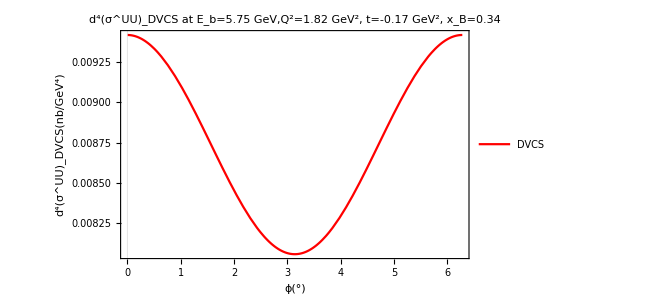

```mathematica
Plot[
{
ConvertGeVMinus6ToNbGevMinus4[CrossSectionPrefactor[qSquared,xBjorken,ϵKinematics,yKinematics] 1/2(DVCSContribution[leptonλPlus,unpolarizedTargetΛ,qSquared,xBjorken,hadronMomentumT,ϕ,ϵKinematics,yKinematics,ξSkewness,KKinematics,ℋ,ℋT,ℰ,ℰT]+DVCSContribution[leptonλMinus,unpolarizedTargetΛ,qSquared,xBjorken,hadronMomentumT,ϕ,ϵKinematics,yKinematics,ξSkewness,KKinematics,ℋ,ℋT,ℰ,ℰT])
]
},
{ϕ,0,2π},
PlotLegends->Placed[
LineLegend[
{
"DVCS"
},
LegendLayout->{
"Row",
1
}
],{0.85, 0.70}
],
PlotStyle->{Red},
FrameLabel->{"ϕ(°)","d^4(σ^UU)_DVCS(nb/GeV^4)"},
PlotLabel->"d^4(σ^UU)_DVCS at E_b=5.75 GeV,Q^2=1.82 GeV^2, t=-0.17 GeV^2, x_B=0.34",
PlotTheme->"Scientific"
]
```

#### (#6.2.1.2): d^4(σ^(+U))_DVCS | Pure DVCS

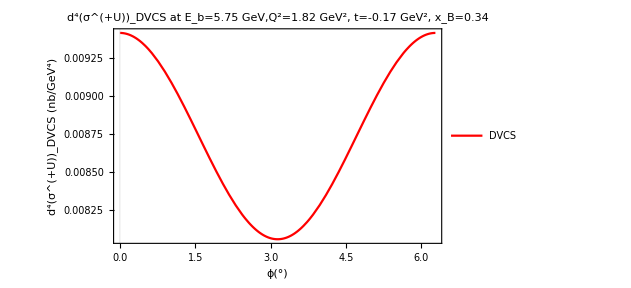

```mathematica
Plot[
{
ConvertGeVMinus6ToNbGevMinus4[CrossSectionPrefactor[qSquared,xBjorken,ϵKinematics,yKinematics]
DVCSContribution[leptonλPlus,unpolarizedTargetΛ,qSquared,xBjorken,hadronMomentumT,ϕ,ϵKinematics,yKinematics,ξSkewness,KKinematics,ℋ,ℋT,ℰ,ℰT]
]
},
{ϕ,0,2π},
PlotLegends->Placed[
LineLegend[
{
"DVCS"
},
LegendLayout->{
"Row",
1
}
],{0.85, 0.70}
],
PlotStyle->{Red},
FrameLabel->{"ϕ(°)","d^4(σ^(+U))_DVCS (nb/GeV^4)"},
PlotLabel->"d^4(σ^(+U))_DVCS at E_b=5.75 GeV,Q^2=1.82 GeV^2, t=-0.17 GeV^2, x_B=0.34",
PlotTheme->"Scientific"
]
```

#### (#6.2.1.3): d^4(σ^-U)_DVCS | Pure DVCS

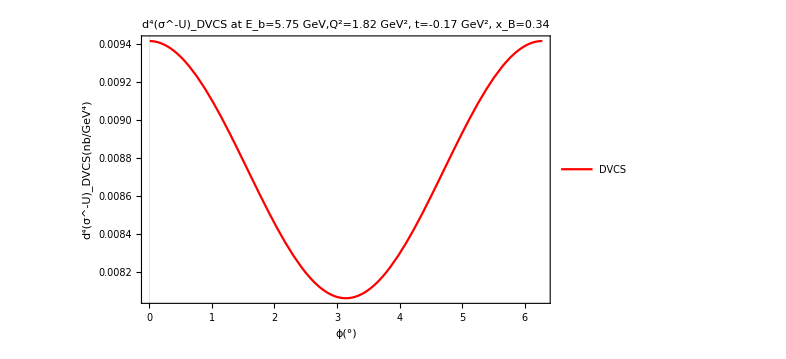

```mathematica
Plot[
{
ConvertGeVMinus6ToNbGevMinus4[
CrossSectionPrefactor[qSquared,xBjorken,ϵKinematics,yKinematics]
DVCSContribution[leptonλMinus,unpolarizedTargetΛ,qSquared,xBjorken,hadronMomentumT,ϕ,ϵKinematics,yKinematics,ξSkewness,KKinematics,ℋ,ℋT,ℰ,ℰT]
]
},
{ϕ,0,2π},
PlotLegends->Placed[
LineLegend[
{
"DVCS"
},
LegendLayout->{
"Row",
1
}
],{0.85, 0.70}
],
PlotStyle->{Red},
FrameLabel->{"ϕ(°)","d^4(σ^-U)_DVCS(nb/GeV^4)"},
PlotLabel->"d^4(σ^-U)_DVCS at E_b=5.75 GeV,Q^2=1.82 GeV^2, t=-0.17 GeV^2, x_B=0.34",
PlotTheme->"Scientific"
]
```

#### (#6.2.1.4): d^4(σ^UL)_DVCS | Pure DVCS

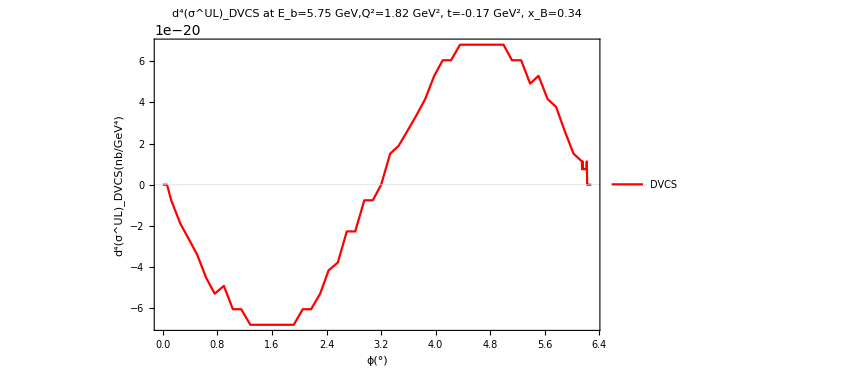

```mathematica
Plot[
{
ConvertGeVMinus6ToNbGevMinus4[CrossSectionPrefactor[qSquared,xBjorken,ϵKinematics,yKinematics] 1/2(DVCSContribution[leptonλPlus,longitudinallyPolarizedTargetΛ,qSquared,xBjorken,hadronMomentumT,ϕ,ϵKinematics,yKinematics,ξSkewness,KKinematics,ℋ,ℋT,ℰ,ℰT]+DVCSContribution[leptonλMinus,longitudinallyPolarizedTargetΛ,qSquared,xBjorken,hadronMomentumT,ϕ,ϵKinematics,yKinematics,ξSkewness,KKinematics,ℋ,ℋT,ℰ,ℰT])
]
},
{ϕ,0,2π},
PlotLegends->Placed[
LineLegend[
{
"DVCS"
},
LegendLayout->{
"Row",
1
}
],{0.85, 0.70}
],
PlotStyle->{Red},
FrameLabel->{"ϕ(°)","d^4(σ^UL)_DVCS(nb/GeV^4)"},
PlotLabel->"d^4(σ^UL)_DVCS at E_b=5.75 GeV,Q^2=1.82 GeV^2, t=-0.17 GeV^2, x_B=0.34",
PlotTheme->"Scientific"
]
```

### (#6.2.2): Pure DVCS Harmonic Contributions:

#### (#6.2.2.1): d^4(σ^UU)_DVCS | Harmonic Contributions

```mathematica
Plot[
{
1/2(cODVCS[leptonλPlus,unpolarizedTargetΛ,qSquared,xBjorken,hadronMomentumT,ϵKinematics,yKinematics,KKinematics,ℋ,ℋT,ℰ,ℰT,Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT],EffectiveFormFactor[ξSkewness,ℋ],EffectiveFormFactor[ξSkewness,ℋT],EffectiveFormFactor[ξSkewness,ℰ],EffectiveFormFactor[ξSkewness,ℰT],EffectiveFormFactor[ξSkewness,Conjugate[ℋ]],EffectiveFormFactor[ξSkewness,Conjugate[ℋT]],EffectiveFormFactor[ξSkewness,Conjugate[ℰ]],EffectiveFormFactor[ξSkewness,Conjugate[ℰT]]]+cODVCS[leptonλMinus,unpolarizedTargetΛ,qSquared,xBjorken,hadronMomentumT,ϵKinematics,yKinematics,KKinematics,ℋ,ℋT,ℰ,ℰT,Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT],EffectiveFormFactor[ξSkewness,ℋ],EffectiveFormFactor[ξSkewness,ℋT],EffectiveFormFactor[ξSkewness,ℰ],EffectiveFormFactor[ξSkewness,ℰT],EffectiveFormFactor[ξSkewness,Conjugate[ℋ]],EffectiveFormFactor[ξSkewness,Conjugate[ℋT]],EffectiveFormFactor[ξSkewness,Conjugate[ℰ]],EffectiveFormFactor[ξSkewness,Conjugate[ℰT]]]),
1/2(c1DVCS[leptonλPlus,unpolarizedTargetΛ,qSquared,xBjorken,hadronMomentumT,ϵKinematics,yKinematics,KKinematics,EffectiveFormFactor[ξSkewness,ℋ],EffectiveFormFactor[ξSkewness,ℋT],EffectiveFormFactor[ξSkewness,ℰ],EffectiveFormFactor[ξSkewness,ℰT],Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT]]+c1DVCS[leptonλMinus,unpolarizedTargetΛ,qSquared,xBjorken,hadronMomentumT,ϵKinematics,yKinematics,KKinematics,EffectiveFormFactor[ξSkewness,ℋ],EffectiveFormFactor[ξSkewness,ℋT],EffectiveFormFactor[ξSkewness,ℰ],EffectiveFormFactor[ξSkewness,ℰT],Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT]])Cos[1(π-ϕ)],1/2(c2DVCS[leptonλPlus,unpolarizedTargetΛ,qSquared,xBjorken,hadronMomentumT,ϵKinematics,yKinematics,KKinematics,EffectiveFormFactor[ξSkewness,ℋ],EffectiveFormFactor[ξSkewness,ℋT],EffectiveFormFactor[ξSkewness,ℰ],EffectiveFormFactor[ξSkewness,ℰT],Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT]]+c2DVCS[leptonλMinus,unpolarizedTargetΛ,qSquared,xBjorken,hadronMomentumT,ϵKinematics,yKinematics,KKinematics,EffectiveFormFactor[ξSkewness,ℋ],EffectiveFormFactor[ξSkewness,ℋT],EffectiveFormFactor[ξSkewness,ℰ],EffectiveFormFactor[ξSkewness,ℰT],Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT]])Cos[2(π-ϕ)],
1/2(s1DVCS[leptonλPlus,unpolarizedTargetΛ,qSquared,xBjorken,hadronMomentumT,ϵKinematics,yKinematics,KKinematics,EffectiveFormFactor[ξSkewness,ℋ],EffectiveFormFactor[ξSkewness,ℋT],EffectiveFormFactor[ξSkewness,ℰ],EffectiveFormFactor[ξSkewness,ℰT],Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT]]+s1DVCS[leptonλMinus,unpolarizedTargetΛ,qSquared,xBjorken,hadronMomentumT,ϵKinematics,yKinematics,KKinematics,EffectiveFormFactor[ξSkewness,ℋ],EffectiveFormFactor[ξSkewness,ℋT],EffectiveFormFactor[ξSkewness,ℰ],EffectiveFormFactor[ξSkewness,ℰT],Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT]])Sin[1(π- ϕ)],1/2(s2DVCS[leptonλPlus,unpolarizedTargetΛ,qSquared,xBjorken,hadronMomentumT,ϵKinematics,yKinematics,KKinematics,EffectiveFormFactor[ξSkewness,ℋ],EffectiveFormFactor[ξSkewness,ℋT],EffectiveFormFactor[ξSkewness,ℰ],EffectiveFormFactor[ξSkewness,ℰT],Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT]]+s2DVCS[leptonλMinus,unpolarizedTargetΛ,qSquared,xBjorken,hadronMomentumT,ϵKinematics,yKinematics,KKinematics,EffectiveFormFactor[ξSkewness,ℋ],EffectiveFormFactor[ξSkewness,ℋT],EffectiveFormFactor[ξSkewness,ℰ],EffectiveFormFactor[ξSkewness,ℰT],Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT]])Sin[2(π- ϕ)]
},
{ϕ,0,2π},
PlotLegends->Placed[
LineLegend[
{
"c_0^DVCS",
"c_1^DVCScos(π-ϕ)",
"c_2^DVCScos(2(π-ϕ))",
"s_1^DVCSsin(π-ϕ)",
"s_2^DVCSsin(2(π-ϕ))"
},
LegendLayout->{
"Row",
5
}
],{0.85, 0.70}
],
PlotStyle->{Red, Orange,Green,Cyan, Purple},
FrameLabel->{"ϕ(°)","d^4(σ^UU)_DVCS(nb/GeV^4) Only Harmonics"},
PlotLabel->"d^4(σ^UU)_INT at E_b=5.75 GeV,Q^2=1.82 GeV^2, t=-0.17 GeV^2, x_B=0.34",
PlotTheme->"Scientific"
]
```

-Graphics-

#### (#6.2.2.2): d^4(σ^(+U))_DVCS | Harmonic Contributions

```mathematica
Plot[
{
cODVCS[leptonλPlus,unpolarizedTargetΛ,qSquared,xBjorken,hadronMomentumT,ϵKinematics,yKinematics,KKinematics,ℋ,ℋT,ℰ,ℰT,Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT],EffectiveFormFactor[ξSkewness,ℋ],EffectiveFormFactor[ξSkewness,ℋT],EffectiveFormFactor[ξSkewness,ℰ],EffectiveFormFactor[ξSkewness,ℰT],EffectiveFormFactor[ξSkewness,Conjugate[ℋ]],EffectiveFormFactor[ξSkewness,Conjugate[ℋT]],EffectiveFormFactor[ξSkewness,Conjugate[ℰ]],EffectiveFormFactor[ξSkewness,Conjugate[ℰT]]],
c1DVCS[leptonλPlus,unpolarizedTargetΛ,qSquared,xBjorken,hadronMomentumT,ϵKinematics,yKinematics,KKinematics,EffectiveFormFactor[ξSkewness,ℋ],EffectiveFormFactor[ξSkewness,ℋT],EffectiveFormFactor[ξSkewness,ℰ],EffectiveFormFactor[ξSkewness,ℰT],Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT]]Cos[1(π-ϕ)],c2DVCS[leptonλPlus,unpolarizedTargetΛ,qSquared,xBjorken,hadronMomentumT,ϵKinematics,yKinematics,KKinematics,EffectiveFormFactor[ξSkewness,ℋ],EffectiveFormFactor[ξSkewness,ℋT],EffectiveFormFactor[ξSkewness,ℰ],EffectiveFormFactor[ξSkewness,ℰT],Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT]]Cos[2(π-ϕ)],
s1DVCS[leptonλPlus,unpolarizedTargetΛ,qSquared,xBjorken,hadronMomentumT,ϵKinematics,yKinematics,KKinematics,EffectiveFormFactor[ξSkewness,ℋ],EffectiveFormFactor[ξSkewness,ℋT],EffectiveFormFactor[ξSkewness,ℰ],EffectiveFormFactor[ξSkewness,ℰT],Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT]]Sin[1(π- ϕ)],s2DVCS[leptonλPlus,unpolarizedTargetΛ,qSquared,xBjorken,hadronMomentumT,ϵKinematics,yKinematics,KKinematics,EffectiveFormFactor[ξSkewness,ℋ],EffectiveFormFactor[ξSkewness,ℋT],EffectiveFormFactor[ξSkewness,ℰ],EffectiveFormFactor[ξSkewness,ℰT],Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT]]Sin[2(π- ϕ)]
},
{ϕ,0,2π},
PlotLegends->Placed[
LineLegend[
{
"c_0^DVCS",
"c_1^DVCScos(π-ϕ)",
"c_2^DVCScos(2(π-ϕ))",
"s_1^DVCSsin(π-ϕ)",
"s_2^DVCSsin(2(π-ϕ))"
},
LegendLayout->{
"Row",
5
}
],{0.85, 0.70}
],
PlotStyle->{Red, Orange,Green,Cyan, Purple},
FrameLabel->{"ϕ(°)","d^4(σ^(+U))_DVCS(nb/GeV^4) Only Harmonics"},
PlotLabel->"d^4(σ^(+U))_DVCS at E_b=5.75 GeV,Q^2=1.82 GeV^2, t=-0.17 GeV^2, x_B=0.34",
PlotTheme->"Scientific"
]
```

-Graphics-

#### (#6.2.2.3): d^4(σ^-U)_DVCS | Harmonic Contributions

```mathematica
Plot[
{
cODVCS[leptonλMinus,unpolarizedTargetΛ,qSquared,xBjorken,hadronMomentumT,ϵKinematics,yKinematics,KKinematics,ℋ,ℋT,ℰ,ℰT,Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT],EffectiveFormFactor[ξSkewness,ℋ],EffectiveFormFactor[ξSkewness,ℋT],EffectiveFormFactor[ξSkewness,ℰ],EffectiveFormFactor[ξSkewness,ℰT],EffectiveFormFactor[ξSkewness,Conjugate[ℋ]],EffectiveFormFactor[ξSkewness,Conjugate[ℋT]],EffectiveFormFactor[ξSkewness,Conjugate[ℰ]],EffectiveFormFactor[ξSkewness,Conjugate[ℰT]]],
c1DVCS[leptonλMinus,unpolarizedTargetΛ,qSquared,xBjorken,hadronMomentumT,ϵKinematics,yKinematics,KKinematics,EffectiveFormFactor[ξSkewness,ℋ],EffectiveFormFactor[ξSkewness,ℋT],EffectiveFormFactor[ξSkewness,ℰ],EffectiveFormFactor[ξSkewness,ℰT],Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT]]Cos[1(π-ϕ)],c2DVCS[leptonλMinus,unpolarizedTargetΛ,qSquared,xBjorken,hadronMomentumT,ϵKinematics,yKinematics,KKinematics,EffectiveFormFactor[ξSkewness,ℋ],EffectiveFormFactor[ξSkewness,ℋT],EffectiveFormFactor[ξSkewness,ℰ],EffectiveFormFactor[ξSkewness,ℰT],Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT]]Cos[2(π-ϕ)],
s1DVCS[leptonλMinus,unpolarizedTargetΛ,qSquared,xBjorken,hadronMomentumT,ϵKinematics,yKinematics,KKinematics,EffectiveFormFactor[ξSkewness,ℋ],EffectiveFormFactor[ξSkewness,ℋT],EffectiveFormFactor[ξSkewness,ℰ],EffectiveFormFactor[ξSkewness,ℰT],Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT]]Sin[1(π- ϕ)],s2DVCS[leptonλMinus,unpolarizedTargetΛ,qSquared,xBjorken,hadronMomentumT,ϵKinematics,yKinematics,KKinematics,EffectiveFormFactor[ξSkewness,ℋ],EffectiveFormFactor[ξSkewness,ℋT],EffectiveFormFactor[ξSkewness,ℰ],EffectiveFormFactor[ξSkewness,ℰT],Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT]]Sin[2(π- ϕ)]
},
{ϕ,0,2π},
PlotLegends->Placed[
LineLegend[
{
"c_0^DVCS",
"c_1^DVCScos(π-ϕ)",
"c_2^DVCScos(2(π-ϕ))",
"s_1^DVCSsin(π-ϕ)",
"s_2^DVCSsin(2(π-ϕ))"
},
LegendLayout->{
"Row",
5
}
],{0.85, 0.70}
],
PlotStyle->{Red, Orange,Green,Cyan, Purple},
FrameLabel->{"ϕ(°)","d^4(σ^-U)_DVCS(nb/GeV^4) Only Harmonics"},
PlotLabel->"d^4(σ^-U)_DVCS at E_b=5.75 GeV,Q^2=1.82 GeV^2, t=-0.17 GeV^2, x_B=0.34",
PlotTheme->"Scientific"
]
```

-Graphics-

#### (#6.2.2.4): d^4(σ^UL)_DVCS | Harmonic Contributions

```mathematica
Plot[
{
1/2(cODVCS[leptonλPlus,longitudinallyPolarizedTargetΛ,qSquared,xBjorken,hadronMomentumT,ϵKinematics,yKinematics,KKinematics,ℋ,ℋT,ℰ,ℰT,Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT],EffectiveFormFactor[ξSkewness,ℋ],EffectiveFormFactor[ξSkewness,ℋT],EffectiveFormFactor[ξSkewness,ℰ],EffectiveFormFactor[ξSkewness,ℰT],EffectiveFormFactor[ξSkewness,Conjugate[ℋ]],EffectiveFormFactor[ξSkewness,Conjugate[ℋT]],EffectiveFormFactor[ξSkewness,Conjugate[ℰ]],EffectiveFormFactor[ξSkewness,Conjugate[ℰT]]]+cODVCS[leptonλMinus,longitudinallyPolarizedTargetΛ,qSquared,xBjorken,hadronMomentumT,ϵKinematics,yKinematics,KKinematics,ℋ,ℋT,ℰ,ℰT,Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT],EffectiveFormFactor[ξSkewness,ℋ],EffectiveFormFactor[ξSkewness,ℋT],EffectiveFormFactor[ξSkewness,ℰ],EffectiveFormFactor[ξSkewness,ℰT],EffectiveFormFactor[ξSkewness,Conjugate[ℋ]],EffectiveFormFactor[ξSkewness,Conjugate[ℋT]],EffectiveFormFactor[ξSkewness,Conjugate[ℰ]],EffectiveFormFactor[ξSkewness,Conjugate[ℰT]]]),
1/2(c1DVCS[leptonλPlus,longitudinallyPolarizedTargetΛ,qSquared,xBjorken,hadronMomentumT,ϵKinematics,yKinematics,KKinematics,EffectiveFormFactor[ξSkewness,ℋ],EffectiveFormFactor[ξSkewness,ℋT],EffectiveFormFactor[ξSkewness,ℰ],EffectiveFormFactor[ξSkewness,ℰT],Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT]]+c1DVCS[leptonλMinus,longitudinallyPolarizedTargetΛ,qSquared,xBjorken,hadronMomentumT,ϵKinematics,yKinematics,KKinematics,EffectiveFormFactor[ξSkewness,ℋ],EffectiveFormFactor[ξSkewness,ℋT],EffectiveFormFactor[ξSkewness,ℰ],EffectiveFormFactor[ξSkewness,ℰT],Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT]])Cos[1(π-ϕ)],1/2(c2DVCS[leptonλPlus,longitudinallyPolarizedTargetΛ,qSquared,xBjorken,hadronMomentumT,ϵKinematics,yKinematics,KKinematics,EffectiveFormFactor[ξSkewness,ℋ],EffectiveFormFactor[ξSkewness,ℋT],EffectiveFormFactor[ξSkewness,ℰ],EffectiveFormFactor[ξSkewness,ℰT],Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT]]+c2DVCS[leptonλMinus,longitudinallyPolarizedTargetΛ,qSquared,xBjorken,hadronMomentumT,ϵKinematics,yKinematics,KKinematics,EffectiveFormFactor[ξSkewness,ℋ],EffectiveFormFactor[ξSkewness,ℋT],EffectiveFormFactor[ξSkewness,ℰ],EffectiveFormFactor[ξSkewness,ℰT],Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT]])Cos[2(π-ϕ)],
1/2(s1DVCS[leptonλPlus,longitudinallyPolarizedTargetΛ,qSquared,xBjorken,hadronMomentumT,ϵKinematics,yKinematics,KKinematics,EffectiveFormFactor[ξSkewness,ℋ],EffectiveFormFactor[ξSkewness,ℋT],EffectiveFormFactor[ξSkewness,ℰ],EffectiveFormFactor[ξSkewness,ℰT],Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT]]+s1DVCS[leptonλMinus,longitudinallyPolarizedTargetΛ,qSquared,xBjorken,hadronMomentumT,ϵKinematics,yKinematics,KKinematics,EffectiveFormFactor[ξSkewness,ℋ],EffectiveFormFactor[ξSkewness,ℋT],EffectiveFormFactor[ξSkewness,ℰ],EffectiveFormFactor[ξSkewness,ℰT],Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT]])Sin[1(π- ϕ)],1/2(s2DVCS[leptonλPlus,longitudinallyPolarizedTargetΛ,qSquared,xBjorken,hadronMomentumT,ϵKinematics,yKinematics,KKinematics,EffectiveFormFactor[ξSkewness,ℋ],EffectiveFormFactor[ξSkewness,ℋT],EffectiveFormFactor[ξSkewness,ℰ],EffectiveFormFactor[ξSkewness,ℰT],Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT]]+s2DVCS[leptonλMinus,longitudinallyPolarizedTargetΛ,qSquared,xBjorken,hadronMomentumT,ϵKinematics,yKinematics,KKinematics,EffectiveFormFactor[ξSkewness,ℋ],EffectiveFormFactor[ξSkewness,ℋT],EffectiveFormFactor[ξSkewness,ℰ],EffectiveFormFactor[ξSkewness,ℰT],Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT]])Sin[2(π- ϕ)]
},
{ϕ,0,2π},
PlotLegends->Placed[
LineLegend[
{
"c_0^DVCS",
"c_1^DVCScos(π-ϕ)",
"c_2^DVCScos(2(π-ϕ))",
"s_1^DVCSsin(π-ϕ)",
"s_2^DVCSsin(2(π-ϕ))"
},
LegendLayout->{
"Row",
5
}
],{0.85, 0.70}
],
PlotStyle->{Red, Orange,Green,Cyan, Purple},
FrameLabel->{"ϕ(°)","d^4(σ^UL)_DVCS(nb/GeV^4) Only Harmonics"},
PlotLabel->"d^4(σ^UL)_DVCS at E_b=5.75 GeV,Q^2=1.82 GeV^2, t=-0.17 GeV^2, x_B=0.34",
PlotTheme->"Scientific"
]
```

-Graphics-

#### (#6.2.2.4): d^4(σ^(+L))_DVCS | Harmonic Contributions

```mathematica
Plot[
{
cODVCS[leptonλPlus,longitudinallyPolarizedTargetΛ,qSquared,xBjorken,hadronMomentumT,ϵKinematics,yKinematics,KKinematics,ℋ,ℋT,ℰ,ℰT,Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT],EffectiveFormFactor[ξSkewness,ℋ],EffectiveFormFactor[ξSkewness,ℋT],EffectiveFormFactor[ξSkewness,ℰ],EffectiveFormFactor[ξSkewness,ℰT],EffectiveFormFactor[ξSkewness,Conjugate[ℋ]],EffectiveFormFactor[ξSkewness,Conjugate[ℋT]],EffectiveFormFactor[ξSkewness,Conjugate[ℰ]],EffectiveFormFactor[ξSkewness,Conjugate[ℰT]]],
c1DVCS[leptonλPlus,longitudinallyPolarizedTargetΛ,qSquared,xBjorken,hadronMomentumT,ϵKinematics,yKinematics,KKinematics,EffectiveFormFactor[ξSkewness,ℋ],EffectiveFormFactor[ξSkewness,ℋT],EffectiveFormFactor[ξSkewness,ℰ],EffectiveFormFactor[ξSkewness,ℰT],Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT]]Cos[1(π-ϕ)],c2DVCS[leptonλPlus,longitudinallyPolarizedTargetΛ,qSquared,xBjorken,hadronMomentumT,ϵKinematics,yKinematics,KKinematics,EffectiveFormFactor[ξSkewness,ℋ],EffectiveFormFactor[ξSkewness,ℋT],EffectiveFormFactor[ξSkewness,ℰ],EffectiveFormFactor[ξSkewness,ℰT],Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT]]Cos[2(π-ϕ)],
s1DVCS[leptonλPlus,longitudinallyPolarizedTargetΛ,qSquared,xBjorken,hadronMomentumT,ϵKinematics,yKinematics,KKinematics,EffectiveFormFactor[ξSkewness,ℋ],EffectiveFormFactor[ξSkewness,ℋT],EffectiveFormFactor[ξSkewness,ℰ],EffectiveFormFactor[ξSkewness,ℰT],Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT]]Sin[1(π- ϕ)],s2DVCS[leptonλPlus,longitudinallyPolarizedTargetΛ,qSquared,xBjorken,hadronMomentumT,ϵKinematics,yKinematics,KKinematics,EffectiveFormFactor[ξSkewness,ℋ],EffectiveFormFactor[ξSkewness,ℋT],EffectiveFormFactor[ξSkewness,ℰ],EffectiveFormFactor[ξSkewness,ℰT],Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT]]Sin[2(π- ϕ)]
},
{ϕ,0,2π},
PlotLegends->Placed[
LineLegend[
{
"c_0^DVCS",
"c_1^DVCScos(π-ϕ)",
"c_2^DVCScos(2(π-ϕ))",
"s_1^DVCSsin(π-ϕ)",
"s_2^DVCSsin(2(π-ϕ))"
},
LegendLayout->{
"Row",
5
}
],{0.85, 0.70}
],
PlotStyle->{Red, Orange,Green,Cyan, Purple},
FrameLabel->{"ϕ(°)","d^4(σ^(+L))_DVCS(nb/GeV^4) Only Harmonics"},
PlotLabel->"d^4(σ^(+L))_DVCS at E_b=5.75 GeV,Q^2=1.82 GeV^2, t=-0.17 GeV^2, x_B=0.34",
PlotTheme->"Scientific"
]
```

-Graphics-

#### (#6.2.2.4): d^4(σ^-L)_DVCS | Harmonic Contributions

```mathematica
Plot[
{
cODVCS[leptonλMinus,longitudinallyPolarizedTargetΛ,qSquared,xBjorken,hadronMomentumT,ϵKinematics,yKinematics,KKinematics,ℋ,ℋT,ℰ,ℰT,Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT],EffectiveFormFactor[ξSkewness,ℋ],EffectiveFormFactor[ξSkewness,ℋT],EffectiveFormFactor[ξSkewness,ℰ],EffectiveFormFactor[ξSkewness,ℰT],EffectiveFormFactor[ξSkewness,Conjugate[ℋ]],EffectiveFormFactor[ξSkewness,Conjugate[ℋT]],EffectiveFormFactor[ξSkewness,Conjugate[ℰ]],EffectiveFormFactor[ξSkewness,Conjugate[ℰT]]],
c1DVCS[leptonλMinus,longitudinallyPolarizedTargetΛ,qSquared,xBjorken,hadronMomentumT,ϵKinematics,yKinematics,KKinematics,EffectiveFormFactor[ξSkewness,ℋ],EffectiveFormFactor[ξSkewness,ℋT],EffectiveFormFactor[ξSkewness,ℰ],EffectiveFormFactor[ξSkewness,ℰT],Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT]]Cos[1(π-ϕ)],c2DVCS[leptonλMinus,longitudinallyPolarizedTargetΛ,qSquared,xBjorken,hadronMomentumT,ϵKinematics,yKinematics,KKinematics,EffectiveFormFactor[ξSkewness,ℋ],EffectiveFormFactor[ξSkewness,ℋT],EffectiveFormFactor[ξSkewness,ℰ],EffectiveFormFactor[ξSkewness,ℰT],Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT]]Cos[2(π-ϕ)],
s1DVCS[leptonλMinus,longitudinallyPolarizedTargetΛ,qSquared,xBjorken,hadronMomentumT,ϵKinematics,yKinematics,KKinematics,EffectiveFormFactor[ξSkewness,ℋ],EffectiveFormFactor[ξSkewness,ℋT],EffectiveFormFactor[ξSkewness,ℰ],EffectiveFormFactor[ξSkewness,ℰT],Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT]]Sin[1(π- ϕ)],s2DVCS[leptonλMinus,longitudinallyPolarizedTargetΛ,qSquared,xBjorken,hadronMomentumT,ϵKinematics,yKinematics,KKinematics,EffectiveFormFactor[ξSkewness,ℋ],EffectiveFormFactor[ξSkewness,ℋT],EffectiveFormFactor[ξSkewness,ℰ],EffectiveFormFactor[ξSkewness,ℰT],Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT]]Sin[2(π- ϕ)]
},
{ϕ,0,2π},
PlotLegends->Placed[
LineLegend[
{
"c_0^DVCS",
"c_1^DVCScos(π-ϕ)",
"c_2^DVCScos(2(π-ϕ))",
"s_1^DVCSsin(π-ϕ)",
"s_2^DVCSsin(2(π-ϕ))"
},
LegendLayout->{
"Row",
5
}
],{0.85, 0.70}
],
PlotStyle->{Red, Orange,Green,Cyan, Purple},
FrameLabel->{"ϕ(°)","d^4(σ^-L)_DVCS(nb/GeV^4) Only Harmonics"},
PlotLabel->"d^4(σ^-L)_DVCS at E_b=5.75 GeV,Q^2=1.82 GeV^2, t=-0.17 GeV^2, x_B=0.34",
PlotTheme->"Scientific"
]
```

-Graphics-

### (#6.2.2): Pure DVCS Amplitude Squared:

## (#6.3): Interference Term: